```mathematica
a=({{1, 0, 0, 0, 0}, {((10000/h)((((-3/40)(10)+3)/h)+(3/80))), (-(20000/h^2)((-3/40)(10)+3)), ((10000/h)((-3/80)+(((-3/40)(10)+3)/h))), 0, 0}, {0, ((10000/h)((((-3/40)(10)+3)/h)+(3/80))), (-(20000/h^2)((-3/40)(10)+3)), ((10000/h)((-3/80)+(((-3/40)(10)+3)/h))), 0}, {0, 0, ((10000/h)((((-3/40)(10)+3)/h)+(3/80))), (-(20000/h^2)((-3/40)(10)+3)), ((10000/h)((-3/80)+(((-3/40)(10)+3)/h)))}, {0, 0, (((10000)(1.5))/(2h)), (-((20000)(1.5))/h), (((30000)(1.5))/(2h))}})
```

{{1,0,0,0,0},{(10000 (3/80+9/(4 h)))/h,-45000/h^2,(10000 (-3/80+9/(4 h)))/h,0,0},{0,(10000 (3/80+9/(4 h)))/h,-45000/h^2,(10000 (-3/80+9/(4 h)))/h,0},{0,0,(10000 (3/80+9/(4 h)))/h,-45000/h^2,(10000 (-3/80+9/(4 h)))/h},{0,0,7500./h,-30000./h,22500./h}}

```mathematica
b=({{0}, {-50}, {-50}, {-50}, {0}})
```

{{0},{-50},{-50},{-50},{0}}

```mathematica
(*let*) h=.1
```

0.1

```mathematica
LinearSolve[a,b]
```

{{1.05631×10^-19},{0.0000782615},{0.000134077},{0.000167522},{0.00017867}}

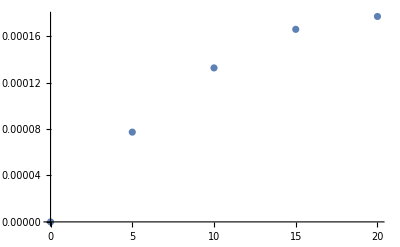

```mathematica
ListPlot[{{0,0},{5,0.0000772985097032464},{10,0.00013259579016788376},{15,0.00016581838153001012},{20,0.0001768925786507189}}]
```

```mathematica
(*makes logical sense*)
```